```mathematica
Solve[{kdel-k1 L R +kminus1 P  - kdeg R==0,k1 L R - kminus1 P - kdegstar P==0},{R,P}]
```

{{R→(kdel (kdegstar+kminus1))/(kdeg kdegstar+kdeg kminus1+k1 kdegstar L),P→(k1 kdel L)/(kdeg kdegstar+kdeg kminus1+k1 kdegstar L)}}

```mathematica
k1=1;kminus1=10;kdeg=0.01;
L=2;
kdegstar=0.35;
RT = 4 10^5;
kdel=RT kdeg
NDSolve[{R'[t] ==kdel-k1 L R[t]+kminus1 P [t] - kdeg R[t],P'[t]==k1 L R [t]- kminus1 P[t] - kdegstar  P[t],R[0]==0,P[0]==0},{R,P},{t,0,100}][[1,2,2]]
```

4000.

InterpolatingFunction[…]

```mathematica
fSampleP[t1__,L_,RT_,kdegstar_,k1_,kminus1_,kdeg_]:=Block[{sols=NDSolve[{R'[t] ==kdel-k1 L R[t]+kminus1 P [t] - kdeg R[t],P'[t]==k1 L R [t]- kminus1 P[t] - kdegstar  P[t],R[0]==0,P[0]==0},{R,P},{t,0,1000}]},sols[[1,2,2]][#]&/@t1]
```

```mathematica
Mean@GammaDistribution[a,b]
```

a b

```mathematica
StandardDeviation@GammaDistribution[a,b]
```

√a b

```mathematica
Solve[{μ==a b,σ==√a b},{a,b}]
```

{{a→μ^2/σ^2,b→σ^2/μ}}

```mathematica
fGamma[μ_,σ_]:=GammaDistribution[μ^2/σ^2,σ^2/μ]
```

```mathematica
fSamplePs[t1__,L_,k1_,kminus1_,kdeg_]:=Block[{RT=RandomVariate[fGamma[4 10^5,1.27 10^5],{1}][[1]],X=RandomVariate[fGamma[0.2,0.16],{1}][[1]],kdegstar},kdegstar=0.55-X;While[Or[RT>8 10^5 ,RT<2.5 10^5],RT=RandomVariate[fGamma[4 10^5,1.27 10^5],{1}][[1]]];While[Or[kdegstar<0.1,kdegstar>0.5],X=RandomVariate[fGamma[0.2,0.16],{1}][[1]];kdegstar=0.55-X];fSampleP[t1,L,RT,kdegstar,k1,kminus1,kdeg]]
```

```mathematica
samples2=Table[fSamplePs[{1,1000},2,1,10,0.01],{1000}];
samples10=Table[fSamplePs[{1,1000},10,1,10,0.01],{1000}];
```

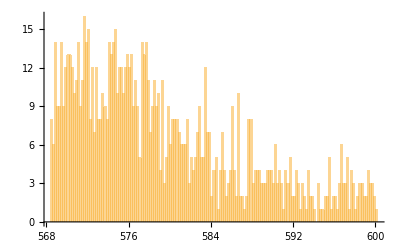

```mathematica
Histogram[{samples2[[All,1]]},100]
```